Testing Spatial Audio on a Single Plane - 2D

## Determining Delay with Dist. to Ears

Graphical Visualization

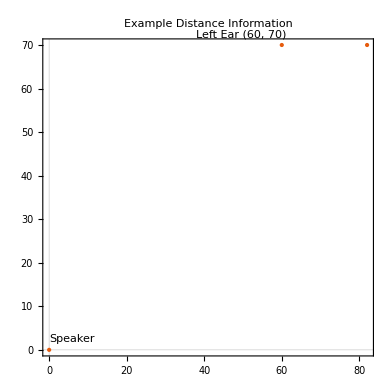

```mathematica
ListPlot[{
Labeled[{0,0},"Speaker"],
Labeled[{60,70}, "Left Ear (60, 70)"],
Labeled[{82,70}, "Right Ear (62, 70)"]
},
PlotTheme->"Scientific",
(*PlotRange->{{0,100},{0,100}},*)
PlotStyle->PointSize[Large],
ScalingFunctions->{Identity,Identity}, 
AspectRatio->1,
PlotRangePadding->10,
PlotLabel->"Example Distance Information"]
```

Assigning Attributes

```mathematica
distanceLeftEar = Quantity[√(60.^2+70.^2),"centimeters"]
distanceRightEar = Quantity[√(62.^2+70.^2), "centimeters"]
(*Angle Between Speaker and X-axis when connected as Right Triangle with Ear*)
thetaLeftEar =Quantity[ArcTan[70./60.] ,"radians"]
thetaRightEar =Quantity[ArcTan[70./62.], "radians"]
```

92.1954 cm

93.5094 cm

0.86217 rad

0.84593 rad

Speed of Sound

```mathematica
speedOfSound =StandardAtmosphereData[Quantity[0, "feet"],"SoundSpeed"]
```

340.29 m/s

Determining Delays

```mathematica
delayLeftEar=distanceLeftEar/speedOfSound
delayRightEar = distanceRightEar / speedOfSound
```

0.00270932 s

0.00274793 s

## Working with Audio Functions to Channel Delay

```mathematica
sampleAudio=Import["/Users/shubhamkumar/Downloads/prenks/Serene Queen - LDR.mp3"]
```

```mathematica
(*Doesn't Work, Stereo not split into Mono for each Channel*)
AudioChannelSeparate[sampleAudio]
```

{,}

Visualizing Audio and Trimming For Faster Processing

-Graphics-

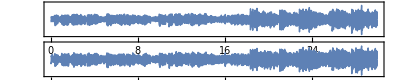

2

```mathematica
sampleAudioTrimmed = AudioTrim[sampleAudio, {10,40}]
Spectrogram[sampleAudioTrimmed]
AudioPlot[sampleAudioTrimmed]
AudioChannels[sampleAudioTrimmed]
```

Panning Test

```mathematica
leftAudio = AudioPan[sampleAudioTrimmed,-1.]
rightAudio = AudioPan[sampleAudioTrimmed, 1.]
```

```mathematica
AudioChannelCombine[{leftAudio, rightAudio}]
```

Delaying Audio For Each Channel

```mathematica
delayedLeftAudio = AudioDelay[leftAudio,delayLeftEar]
delayedRightAudio= AudioDelay[rightAudio,delayRightEar]
(*Making Sure Delay Worked*)
Duration@{delayedLeftAudio, delayedRightAudio, leftAudio, rightAudio}
```

{30.0027 s,30.0027 s,30. s,30. s}

```mathematica
spatial2dAudioTrimmed = AudioChannelCombine[{delayedRightAudio, delayedLeftAudio}]
```

Checking Differences

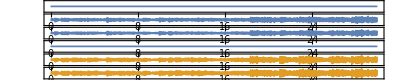

{4,2}

```mathematica
AudioPlot@{spatial2dAudioTrimmed, sampleAudioTrimmed}
AudioChannels@{spatial2dAudioTrimmed, sampleAudioTrimmed}
```

## Functional Implementation

Combining Processes from Previous Sections + Adding in Audio Amplification

```mathematica
PlotPoint2dAudio[speakerPoint_, leftEar_, rightEar_]:=
Module[{speakerPointLoc=speakerPoint, leftEarPointLoc=leftEar, rightEarPointLoc=rightEar},
(*Bruh why do arrays start at 1*)
(*Print[speakerPointLoc[[0]]];*)
ListPlot[{
Labeled[{speakerPointLoc[[1]], speakerPointLoc[[2]]},"Speaker"],
Labeled[{leftEarPointLoc[[1]], leftEarPointLoc[[2]]}, "Left Ear"],
Labeled[{rightEarPointLoc[[1]], rightEarPointLoc[[2]]}, "Right Ear"]
},
PlotTheme->"Scientific",
(*PlotRange->{{0,100},{0,100}},*)
PlotStyle->PointSize[Large],
ScalingFunctions->{Identity,Identity}, 
AspectRatio->1,
PlotRangePadding->10,
PlotLabel->"Distance Information"]
]
```

```mathematica
Point2dAudioV1[file_, speakerPoint_, leftEar_, rightEar_, amplificationProportion_, trimStart_, trimEnd_]:=
Module[{fileLoc=file, speakerPointLoc=speakerPoint, leftEarPointLoc=leftEar, rightEarPointLoc=rightEar, k=amplificationProportion, t1=trimStart, t2=trimEnd},
(*Trimming Raw Audio & Separating Audio for each Channel*)
rawAudioData = Import[fileLoc];
trimmedRawAudioData = AudioNormalize[AudioTrim[rawAudioData,{t1, t2}]];
leftAudioData = AudioPan[trimmedRawAudioData,-1.];
rightAudioData = AudioPan[trimmedRawAudioData, 1.];

(*Calculating Delays*)
leftEarDistanceFromSpeaker = Quantity[√((leftEarPointLoc[[1]]-speakerPointLoc[[1]])^2.+(leftEarPointLoc[[2]]-speakerPointLoc[[2]])^2.), "centimeters"];
rightEarDistanceFromSpeaker = Quantity[√((rightEarPointLoc[[1]]-speakerPointLoc[[1]])^2.+(rightEarPointLoc[[2]]-speakerPointLoc[[2]])^2.), "centimeters"];
speedOfSound = StandardAtmosphereData[Quantity[0, "feet"],"SoundSpeed"];
leftEarAudioDelay = leftEarDistanceFromSpeaker/speedOfSound;
rightEarAudioDelay = rightEarDistanceFromSpeaker/speedOfSound;

(*Debug*)
(*Print["Left Ear Audio Distance:"]; Print[leftEarDistanceFromSpeaker];
Print["Right Ear Audio Distance:"]; Print[rightEarDistanceFromSpeaker];
Print["Left Ear Audio Delay:"]; Print[leftEarAudioDelay];
Print["Right Ear Audio Delay:"]; Print[rightEarAudioDelay];*)

(*Audio Delaying & Attenuation*)
leftEarAudioDelayedData = If[QuantityMagnitude[leftEarDistanceFromSpeaker] ≠ 0, 
AudioAmplify[AudioDelay[leftAudioData, leftEarAudioDelay], QuantityMagnitude[k/leftEarDistanceFromSpeaker]], 
leftAudioData];

rightEarAudioDelayedData = If[QuantityMagnitude[rightEarDistanceFromSpeaker]≠ 0, 
AudioAmplify[AudioDelay[rightAudioData, rightEarAudioDelay], QuantityMagnitude[k/rightEarDistanceFromSpeaker]], 
rightAudioData];

(*Mixing to Generate Final Sound*)
AudioNormalize[AudioChannelCombine[{leftEarAudioDelayedData, rightEarAudioDelayedData}]]
]
```

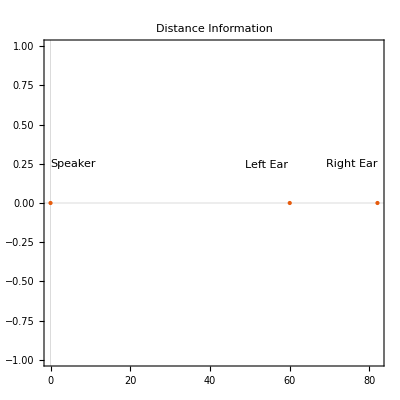

```mathematica
PlotPoint2dAudio[{0,0},{60,0},{82,0}]
```

Function Unit Tests

```mathematica
delayTest = Point2dAudioV1["/Users/shubhamkumar/Downloads/prenks/Thunder - LDR.mp3",{0,0},{60,0},{82,0}, 100, 0, 30]
```

Left channel is indeed louder than the right

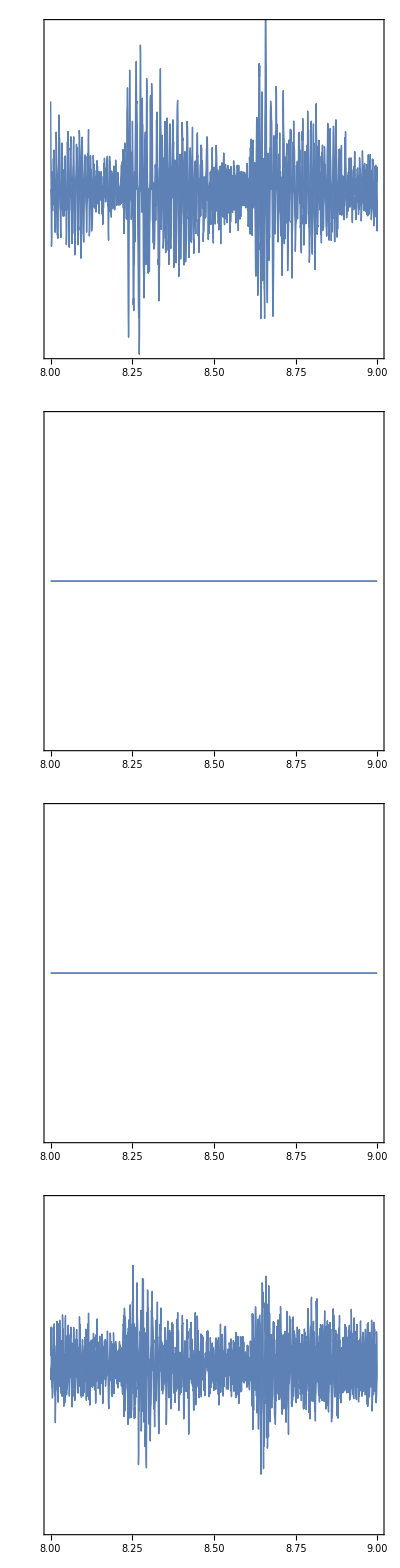

-Graphics-

4

```mathematica
AudioPlot[delayTest, PlotRange->{{8,9},{-0.8, 0.8}}]
Spectrogram[delayTest]
AudioChannels[delayTest]
```

```mathematica
delayTestLoudness =AudioLoudness[delayTest]
```

TimeSeries[…]

Speaker and Ears are all at the same location

```mathematica
(*Lmao don't run this - fixed it, its fine now*)
sanityTest = Point2dAudioV1["/Users/shubhamkumar/Downloads/prenks/Thunder - LDR.mp3",{0,0},{0,0},{0,0}, 100, 0, 30]
```

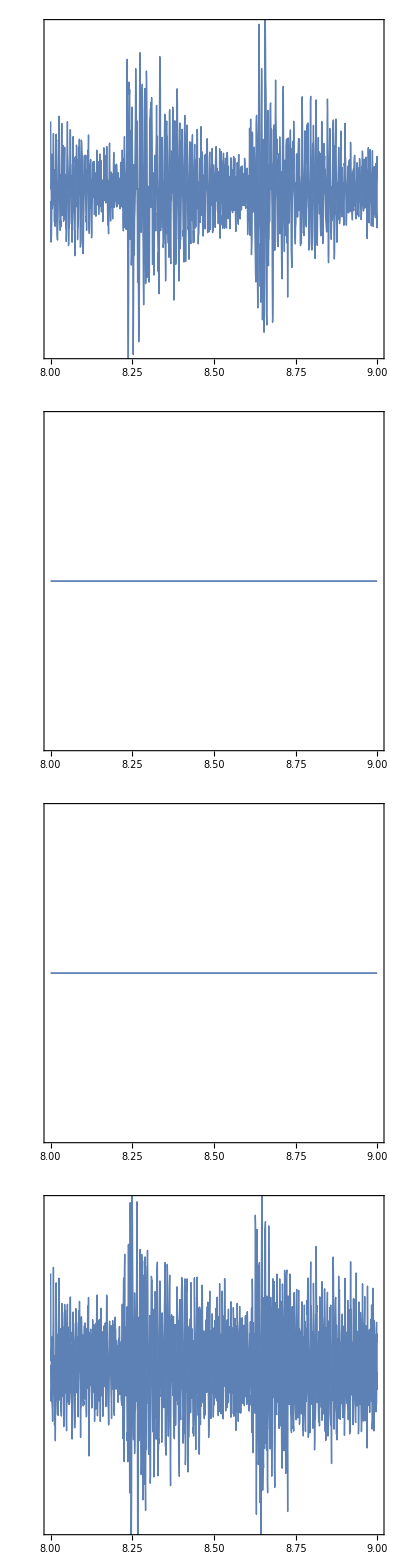

-Graphics-

4

```mathematica
AudioPlot[sanityTest, PlotRange->{{8,9},{-0.8,0.8}}]
Spectrogram[sanityTest]
AudioChannels[sanityTest]
```

```mathematica
sanityTestLoudness = AudioLoudness[sanityTest]
```

TimeSeries[…]

Comparing With Raw Audio - Can’t Quite Tell a Difference but the Audio Plot Shows that there is

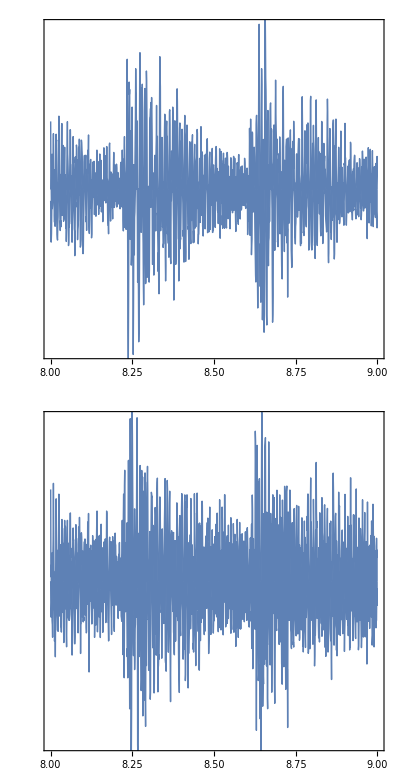

```mathematica
rawAudioComparison=AudioNormalize[AudioTrim[Import["/Users/shubhamkumar/Downloads/prenks/Thunder - LDR.mp3"],{0,30}]]
AudioPlot[rawAudioComparison, PlotRange-> {{8,9},{-0.8, 0.8}}]
```

```mathematica
rawAudioLoudness =AudioLoudness[rawAudioComparison]
```

TimeSeries[…]

Comparing Loudness

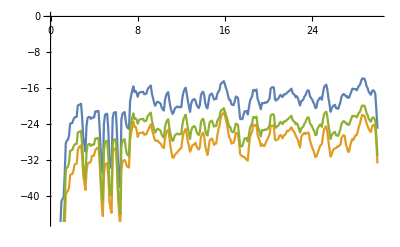

```mathematica
ListLinePlot@{rawAudioLoudness, delayTestLoudness, sanityTestLoudness}
```

## Extend Function to Understand that Head is an Obstacle

## Moving Speaker in 2D Plane

Testing

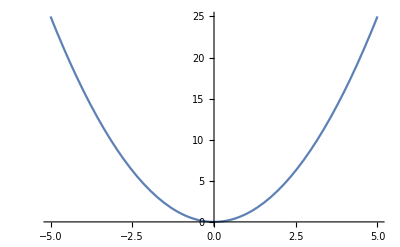

{25.,23.7656,22.5625,21.3906,20.25,19.1406,18.0625,17.0156,16.,15.0156,14.0625,13.1406,12.25,11.3906,10.5625,9.76563,9.,8.26563,7.5625,6.89063,6.25,5.64063,5.0625,4.51563,4.,3.51563,3.0625,2.64063,2.25,1.89063,1.5625,1.26563,1.,0.765625,0.5625,0.390625,0.25,0.140625,0.0625,0.015625,0.,0.015625,0.0625,0.140625,0.25,0.390625,0.5625,0.765625,1.,1.26563,1.5625,1.89063,2.25,2.64063,3.0625,3.51563,4.,4.51563,5.0625,5.64063,6.25,6.89063,7.5625,8.26563,9.,9.76563,10.5625,11.3906,12.25,13.1406,14.0625,15.0156,16.,17.0156,18.0625,19.1406,20.25,21.3906,22.5625,23.7656,25.}

81

```mathematica
Plot[x^2,{x,-5,5}]
locationVals =Table[y^2,{y,-5.,5.,0.125}]
Length[locationVals]
```

Can’t Implement this for my life

```mathematica
(*PlotPath2dAudio[speakerPath_, range_, leftEar_, rightEar_]:=
Module[{speakerPointLoc=speakerPath, rangeLoc=range, leftEarPointLoc=leftEar, rightEarPointLoc=rightEar},
(*Bruh why do arrays start at 1*)
(*Print[speakerPointLoc[[0]]];*)
ListPlot[Echo@Join[{
Legended[{leftEarPointLoc[[1]], leftEarPointLoc[[2]]}, "Left Ear"],
Legended[{rightEarPointLoc[[1]], rightEarPointLoc[[2]]}, "Right Ear"]},
Table[{Sin[n], Sin[2 n]}, {n, 10}]],
PlotTheme->"Scientific",
(*PlotRange->{{0,100},{0,100}},*)
PlotStyle->PointSize[Large],
ScalingFunctions->{Identity,Identity}, 
AspectRatio->1,
PlotRangePadding->10,
PlotLabel->"Distance Information"]
]*)
```

```mathematica
(*PlotPath2dAudio[{0,0},{1,1},{2,2}, {3,3}]*)
```

Visualizing Points

```mathematica
points = Table[{4.n, 100.*Sin[ n]}, {n,0,8Pi, Pi/12}]
Length@points
```

{{0.,0.},{1.0472,25.8819},{2.0944,50.},{3.14159,70.7107},{4.18879,86.6025},{5.23599,96.5926},{6.28319,100.},{7.33038,96.5926},{8.37758,86.6025},{9.42478,70.7107},{10.472,50.},{11.5192,25.8819},{12.5664,0.},{13.6136,-25.8819},{14.6608,-50.},{15.708,-70.7107},{16.7552,-86.6025},{17.8024,-96.5926},{18.8496,-100.},{19.8968,-96.5926},{20.944,-86.6025},{21.9911,-70.7107},{23.0383,-50.},{24.0855,-25.8819},{25.1327,0.},{26.1799,25.8819},{27.2271,50.},{28.2743,70.7107},{29.3215,86.6025},{30.3687,96.5926},{31.4159,100.},{32.4631,96.5926},{33.5103,86.6025},{34.5575,70.7107},{35.6047,50.},{36.6519,25.8819},{37.6991,0.},{38.7463,-25.8819},{39.7935,-50.},{40.8407,-70.7107},{41.8879,-86.6025},{42.9351,-96.5926},{43.9823,-100.},{45.0295,-96.5926},{46.0767,-86.6025},{47.1239,-70.7107},{48.1711,-50.},{49.2183,-25.8819},{50.2655,0.},{51.3127,25.8819},{52.3599,50.},{53.4071,70.7107},{54.4543,86.6025},{55.5015,96.5926},{56.5487,100.},{57.5959,96.5926},{58.6431,86.6025},{59.6903,70.7107},{60.7375,50.},{61.7847,25.8819},{62.8319,0.},{63.8791,-25.8819},{64.9262,-50.},{65.9734,-70.7107},{67.0206,-86.6025},{68.0678,-96.5926},{69.115,-100.},{70.1622,-96.5926},{71.2094,-86.6025},{72.2566,-70.7107},{73.3038,-50.},{74.351,-25.8819},{75.3982,0.},{76.4454,25.8819},{77.4926,50.},{78.5398,70.7107},{79.587,86.6025},{80.6342,96.5926},{81.6814,100.},{82.7286,96.5926},{83.7758,86.6025},{84.823,70.7107},{85.8702,50.},{86.9174,25.8819},{87.9646,0.},{89.0118,-25.8819},{90.059,-50.},{91.1062,-70.7107},{92.1534,-86.6025},{93.2006,-96.5926},{94.2478,-100.},{95.295,-96.5926},{96.3422,-86.6025},{97.3894,-70.7107},{98.4366,-50.},{99.4838,-25.8819},{100.531,0.}}

97

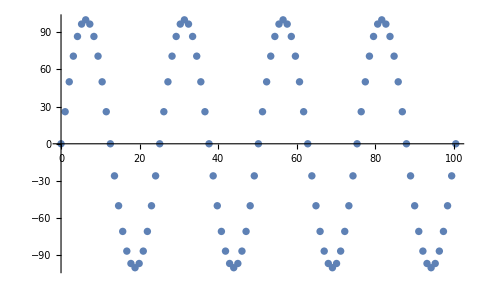

```mathematica
ListPlot[points, ScalingFunctions->{Identity,Identity}]
```

```mathematica
Path2dAudioV1[file_, speakerPath_, leftEar_, rightEar_, amplificationProportion_, duration_]:=
Module[{fileLoc=file, speakerPointLoc=speakerPath, leftEarPointLoc=leftEar, rightEarPointLoc=rightEar, k=amplificationProportion, durationLoc=duration},
subtrimLengths = durationLoc/Length[speakerPath];
AudioJoin[MapIndexed[Point2dAudioV1[file, #1, leftEar, rightEar, amplificationProportion, 30+(First[#2]-1)*subtrimLengths, 30+First[#2]*subtrimLengths]&, speakerPath]]
]
```

```mathematica
out = Path2dAudioV1["/Users/shubhamkumar/Downloads/prenks/Thunder - LDR.mp3", points, {39,-100}, {61, -100}, 100, 10]
```

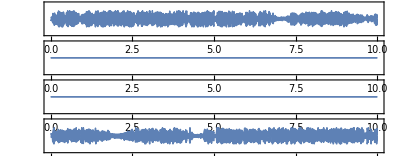

```mathematica
AudioPlot[out, PlotRange->{{0,10},{-2,2}}]
```

```mathematica
AudioNormalize[out]
```